```mathematica
DemoValue[k_]:=allGraphs[k,"colofour"]/.demoValues
```

```mathematica
Table[Labeled [allGraphs[k,"graph"],{allGraphs[k,"colofour"],k,(allGraphs[k,"colofour"]/.demoValues)}],{k,Sort[atomKeys,DemoValue[#1]>DemoValue[#2]&]}]
```

{-Graphics-{v123x4x5,56011,202},-Graphics-{v145x2x3,32441,177},-Graphics-{v145x23,32684,143},-Graphics-{v12x34x5,49216,133},-Graphics-{v125x3x4,49963,121},-Graphics-{v15x2x34,30262,119},-Graphics-{v15x23x4,30496,115},-Graphics-{v1234x5,58288,104},-Graphics-{v123x45,56012,102},-Graphics-{v15x234,30586,102},-Graphics-{v14x23x5,31954,101},-Graphics-{v1x234x5,29857,101},-Graphics-{v125x34,49972,95},-Graphics-{v12x3x45,49208,90},-Graphics-{v1x2x345,29537,87},-Graphics-{v12x3x4x5,49207,82},-Graphics-{v124x3x5,51475,79},-Graphics-{v12x345,49220,78},-Graphics-{v13x2x45,36086,74},-Graphics-{v15x24x3,30334,74},-Graphics-{v1x23x45,29768,74},-Graphics-{v1x23x4x5,29767,74},-Graphics-{v13x25x4,36112,72},-Graphics-{v13x2x4x5,36085,72},-Graphics-{v12345,59048,68},-Graphics-{v1235x4,56770,68},-Graphics-{v1245x3,52232,68},-Graphics-{v1345x2,39014,68},-Graphics-{v134x2x5,38281,66},-Graphics-{v1x25x34,29560,64},-Graphics-{v1x2345,29888,63},-Graphics-{v13x24x5,36166,58},-Graphics-{v15x2x3x4,30253,58},-Graphics-{v1x2x34x5,29533,54},-Graphics-{v12x35x4,49210,53},-Graphics-{v1x2x3x45,29525,53},-Graphics-{v14x25x3,31738,52},-Graphics-{v14x2x3x5,31711,52},-Graphics-{v14x2x35,31714,41},-Graphics-{v1x25x3x4,29551,41},-Graphics-{v135x2x4,36817,40},-Graphics-{v134x25,38308,38},-Graphics-{v1x245x3,29633,35},-Graphics-{v1x235x4,29797,33},-Graphics-{v14x235,31984,30},-Graphics-{v1x2x35x4,29527,30},-Graphics-{v135x24,36898,28},-Graphics-{v13x245,36194,28},-Graphics-{v1x24x3x5,29605,27},-Graphics-{v124x35,51478,25},-Graphics-{v1x24x35,29608,16},-Graphics-{v1x2x3x4x5,29524,0}}

```mathematica
ineqsn=Table[allGraphs[k,"comp"][allGraphs[k,"colofour"],0],{k,Keys[allGraphs]}];Length[ineqsn]
```

1895

```mathematica
countDone=0;ineqsElim2=Monitor[Simplify[Fold[And,ineqsn],Trig->False,ComplexityFunction->MyLeafCount,Assumptions->atomFacts],countDone];Length[ineqsElim2]
```

332

```mathematica
ineqsElim2
```

```mathematica
Map[#[[0]]&,AndToTable[Select[ineqsElim2,Length[ListofVars[#]]==2&]]]//Tally
```

{{Greater,20}}

```mathematica
Select[ineqsElim2,Length[ListofVars[#]]==1&&ToString[#[[0]]]≠"Greater"&]/.repcolofourgraph2
```

True

```mathematica
usedNodes=VertexList[Graph[Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsElim2,Length[ListofVars[#]]==2&]]]]]
```

{0,v1x25x34+v1x2x34x5,v1x245x3+v1x2x3x45,v1x235x4+v1x23x4x5,v15x24x3+v15x2x3x4,v14x235+v14x23x5,v14x23x5+v1x23x4x5,v14x235+v1x235x4,v13x245+v13x2x45,v135x24+v135x2x4,v134x25+v134x2x5,v13x2x45+v1x2x3x45,v13x245+v1x245x3,v135x2x4+v15x2x3x4,v135x24+v15x24x3,v134x2x5+v1x2x34x5,v134x25+v1x25x34,v12x35x4+v12x3x4x5,v124x35+v124x3x5,v124x3x5+v12x3x4x5,v124x35+v12x35x4}

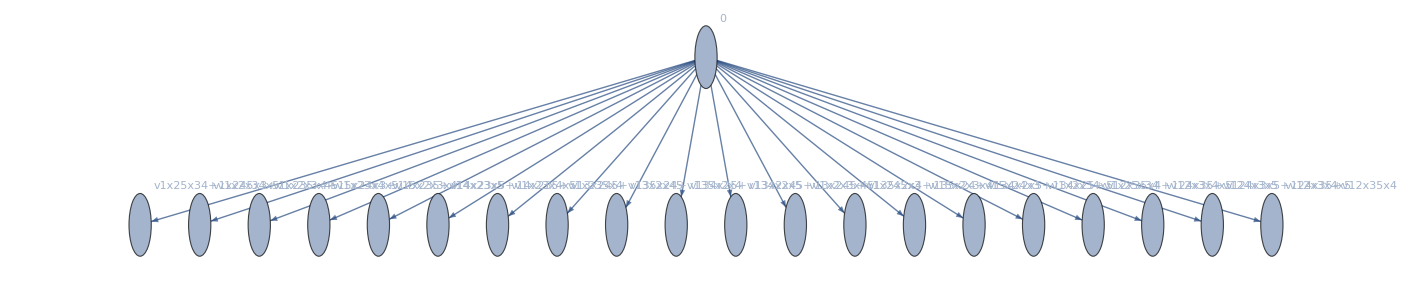

```mathematica
Graph[Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsElim2,Length[ListofVars[#]]==2&]]],VertexLabels->Table[v->(v/.repcolofournullgraph2),{v,usedNodes}]]
```

```mathematica
Select[nullAtomSymbols,!MemberQ[usedNodes,#]&]/.repcolofournullgraph2
```

{-Graphics-p1x2x3x4x50,-Graphics-p1x2x3x451,-Graphics-p1x2x35x43,-Graphics-p1x2x34x59,-Graphics-p1x2x34513,-Graphics-p1x25x3x427,-Graphics-p1x25x3436,-Graphics-p1x24x3x581,-Graphics-p1x24x3584,-Graphics-p1x245x3109,-Graphics-p1x23x4x5243,-Graphics-p1x23x45244,-Graphics-p1x235x4273,-Graphics-p1x234x5333,-Graphics-p1x2345364,-Graphics-p15x2x3x4729,-Graphics-p15x2x34738,-Graphics-p15x24x3810,-Graphics-p15x23x4972,-Graphics-p15x2341062,-Graphics-p14x2x3x52187,-Graphics-p14x2x352190,-Graphics-p14x25x32214,-Graphics-p14x23x52430,-Graphics-p14x2352460,-Graphics-p145x2x32917,-Graphics-p145x233160,-Graphics-p13x2x4x56561,-Graphics-p13x2x456562,-Graphics-p13x25x46588,-Graphics-p13x24x56642,-Graphics-p13x2456670,-Graphics-p135x2x47293,-Graphics-p135x247374,-Graphics-p134x2x58757,-Graphics-p134x258784,-Graphics-p1345x29490,-Graphics-p12x3x4x519683,-Graphics-p12x3x4519684,-Graphics-p12x35x419686,-Graphics-p12x34x519692,-Graphics-p12x34519696,-Graphics-p125x3x420439,-Graphics-p125x3420448,-Graphics-p124x3x521951,-Graphics-p124x3521954,-Graphics-p1245x322708,-Graphics-p123x4x526487,-Graphics-p123x4526488,-Graphics-p1235x427246,-Graphics-p1234x528764,-Graphics-p1234529524}

```mathematica
MobiusGraph2[key_]:=Block[{form=allGraphs[key,"colofournull"], vars, blocks=Association[],c,edges,set, found=Association[]},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[nullAtomKeys,allGraphs[#,"colofournull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[to[[1]],from[[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
Graph[vars,edges,VertexLabels->Table[n->Tooltip[Rotate[(TableForm[{n,Style[Coefficient[form,n],Bold,Blue]},TableAlignments->Center]),Pi/4],found[n,"graph"]],{n,vars}],ImageSize->600,GraphLayout->"LayeredDigraphEmbedding"]
]
```

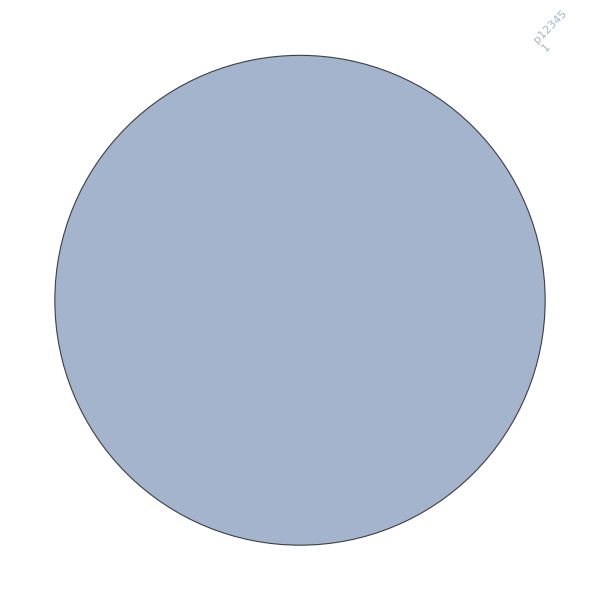

```mathematica
MobiusGraph2[29524]
```